```mathematica
Needs["FormFactors`",NotebookDirectory[]<>"../../packages/FormFactors.wl"]
Needs["Constants`",NotebookDirectory[]<>"../../packages/Constants.wl"]
```

vescape::shdw: Symbol vescape appears in multiple contexts {Constants`,Global`}; definitions in context Constants` may shadow or be shadowed by other definitions.

```mathematica
v0Points = {20,220}10^3
```

{20000,220000}

```mathematica
Clear[vesc]
vesc=11200;
vmaxnuc = vesc/(√(("mN"-mχ)^2/("mN"+mχ)^2))
```

11200/(√((mN-mχ)^2/(mN+mχ)^2))

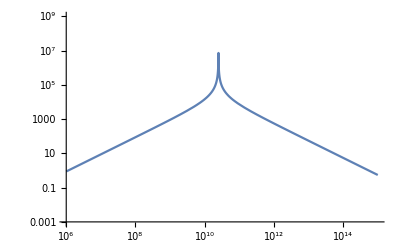

```mathematica
LogLogPlot[vmaxnuc-vesc/.vesc->11000/.mN->2.5 10^10,{mχ,10^6,10^15},PlotRange->{10^-3,10^9}]
```

```mathematica
q->10^6("JpereV")/("c""ℏ")/.SIConstRepl
```

q→5.06161×10^12

(7.78911×10^57 (9.296×10^-26-mχ)^2)/((9.296×10^-26+mχ)^2)

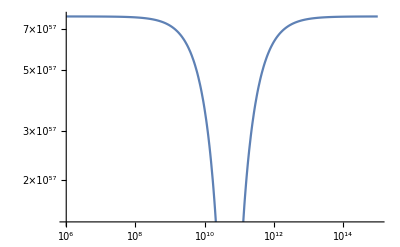

```mathematica
1/vmaxnuc^2 q Zeff[q,#]^2 q^2/(2 "mN")/.#&[FeNucCoeffs]/.q->10^6("JpereV")/("c""ℏ")/.SIConstRepl/.vesc->11200
LogLogPlot[%/.mχ->mχeV("JpereV")/("c")^2/.SIConstRepl,{mχeV,10^6,10^15}]
```

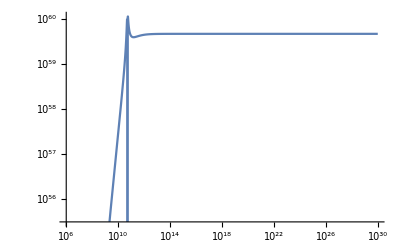

3.41507×10^44

```mathematica
1/(vmaxnuc^2/.vesc->11200)#2 Zeff[#2,#1]^2#2^2/(2 "mN")/.#1&[FeNucCoeffs,((2 (mχ^-1+("mN")^-1)^-1 vmaxnuc)/("ℏ")/.SIConstRepl/.vesc->11200)];
%/.mχ->mχeV("JpereV")/("c")^2/.SIConstRepl;
LogLogPlot[%,{mχeV,10^6,10^30}]
%%/.mχeV->10^7
```

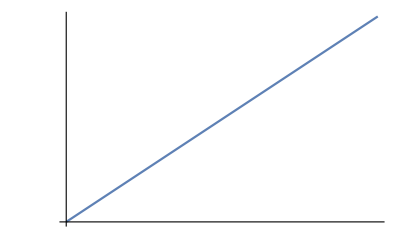

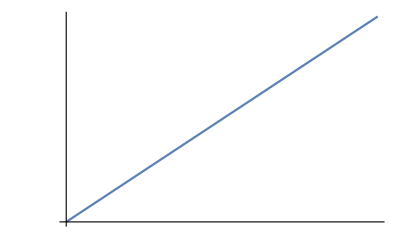

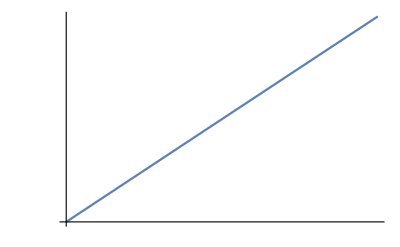

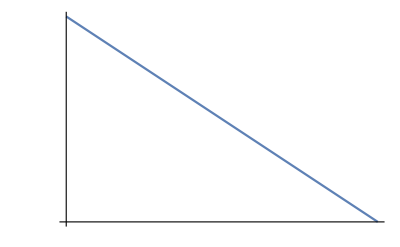

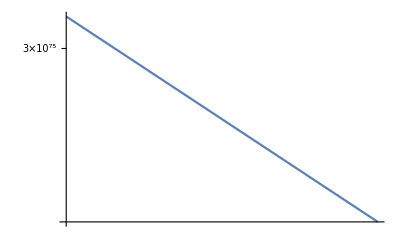

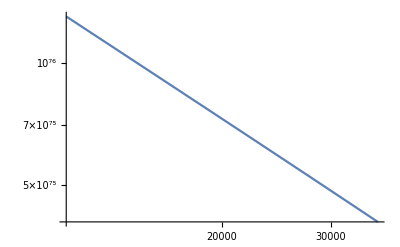

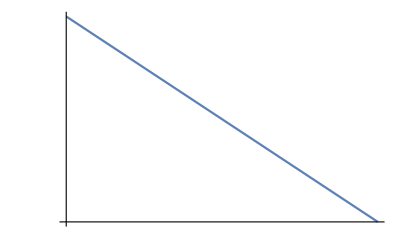

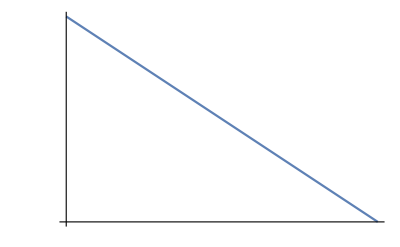

```mathematica
("ℏ")^-2/(vχ^2/.vesc->11200)#2 Zeff[#2,#1]^2/.#1&[FeNucCoeffs,((2 (mχ^-1+("mN")^-1)^-1 vχ)/("ℏ")/.SIConstRepl/.vesc->11200)];
%/.mχ->mχeV("JpereV")/("c")^2/.SIConstRepl;
Do[Print@LogLogPlot[%/.mχeV->10^m,{vχ,vesc,vmaxnuc/.FeNucCoeffs/.mχ->("JpereV")/("c")^2 10^m/.SIConstRepl}(*,PlotRange->{60,80}*)],{m,6,15}]
```

(#2 Zeff[#2,#1]^2)/(ℏ^2 (vmaxnuc^2/.vesc→11200))/.#1/.mχ→(10^m JpereV)/c^2/.SIConstRepl&

6

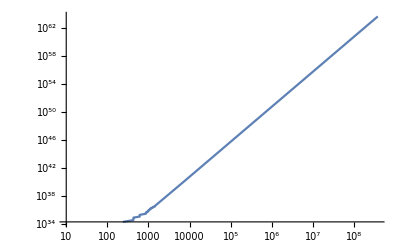

7

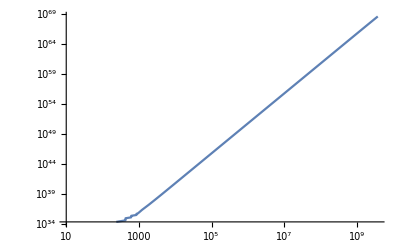

8

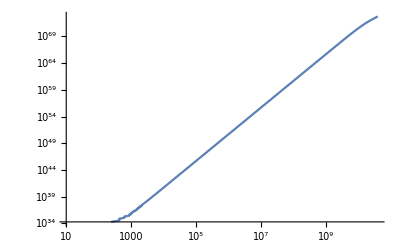

9

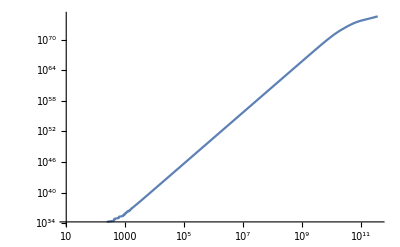

10

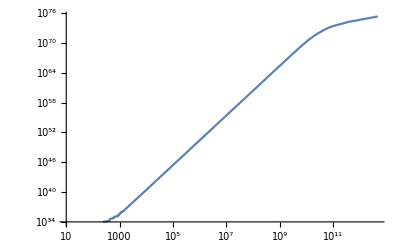

11

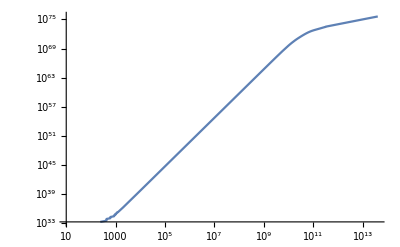

12

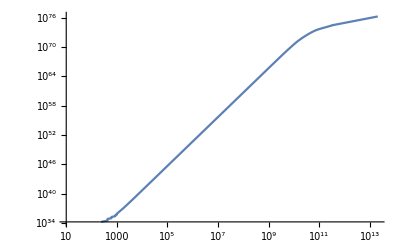

13

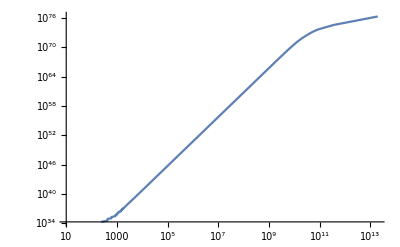

14

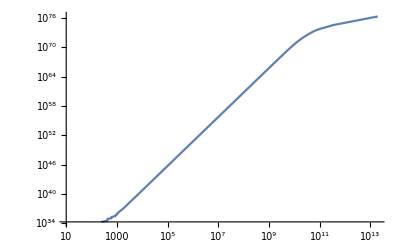

15

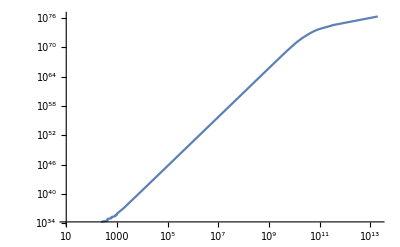

```mathematica
("ℏ")^-2/(vmaxnuc^2/.vesc->11200)#2 Zeff[#2,#1]^2/.#1/.mχ->10^m("JpereV")/("c")^2/.SIConstRepl &
Do[Print@m;Print@LogLogPlot[%[FeNucCoeffs,q]/.mχeV->10^m,{q,10,(2 (mχ^-1+("mN")^-1)^-1 vmaxnuc)/("ℏ")/.mχ->("JpereV")/("c")^2 10^m/.SIConstRepl/.FeNucCoeffs}(*,PlotRange->{60,80}*)],{m,6,15}]
(*With[{m=7},%[FeNucCoeffs,(2 (mχ^-1+("mN")^-1)^-1 vmaxnuc)/("ℏ")/.mχ->("JpereV")/("c")^2 10^m/.SIConstRepl/.FeNucCoeffs]]*)
```